We have an effective Hamiltonian

H_eff=J_x σ_1^x σ_2^x+J_y σ_1^y σ_2^y+J_z σ_1^z σ_2^z+Δ/2(σ_1^z+σ_2^z)

We are going to rewrite this as

H_eff=J_⊥(e^(ⅈϕ/2)σ_1^+σ_2^-+e^(ⅈϕ/2)σ_1^-σ_2^+)+J_z σ_1^z σ_2^z+Δ/2(σ_1^z+σ_2^z)

Up to a constant, in the two-qubit subspace, this matrix is

Heff=(Δ+J_z | 0 | 0 | 0
0 | -J_z | J_⊥e^(ⅈϕ/2) | 0
0 | J_⊥e^(-ⅈϕ/2) | -J_z | 0
0 | 0 | 0 | -Δ+J_z)

```mathematica
Clear[Heff];
Heff={{Δ+Jz, 0, 0, 0},
{0, -Jz, J ⅇ^(ⅈ ϕ/2),0},
{0,J ⅇ^(-ⅈ ϕ/2),-Jz,0},
{0,0,0,-Δ+Jz}};
MatrixForm[Heff]
```

(Jz+Δ | 0 | 0 | 0
0 | -Jz | ⅇ^((ⅈ ϕ)/2) J | 0
0 | ⅇ^(-(ⅈ ϕ)/2) J | -Jz | 0
0 | 0 | 0 | Jz-Δ)

#### Ramsey interferometry

Let us assume a qubit oscillates with a Hamiltonian

H_eff=Δ/2 σ^z

```mathematica
ψ0={0,1};
UH={{1,1},{-1,1}}/√2;
ψ1=UH . ψ0;
ψ2=MatrixExp[-ⅈ Δ {{1,0},{0,-1}}t].ψ1;
ψ3=UH . ψ2;
P0 = ComplexExpand[ψ3[[1]]*ψ3[[1]]]
```

Cos[t Δ]^2

```mathematica
Cos[t Δ]^2
```

Cos[t Δ]^2

#### π/2 pulses

When doing a rotation, the qubit is rapidly driven with an oscillation pulse

H_eff=Δ/2 σ^z+Ω cos(Δ t)σ^x

In the interaction picture with σ^z

ψ(t)=exp(-ⅈ Δσ^z t/2)χ(t)

ⅈ dχ/dt=(H_eff-Δ/2 σ^z)χ=Ω/2 (ⅇ^-ⅈΔt+ⅇ^(+iΔt))(ⅇ^(-ⅈ Δ t)σ^-+ⅇ^(ⅈ Δ t)σ^+)χ≃Ω/2 σ^x χ

ψ(t)=exp(-ⅈ Δ σ^z t/2)exp(-ⅈ ϕ σ^x)ψ(0)

#### Interaction picture with σ^z

H_eff=(J_⊥ⅇ^(ⅈ ϕ/2)σ_1^+σ_2^-+H.c.)+J_z σ_1^z σ_2^z+δ/2(σ_1^z+σ_2^z)

```mathematica
Clear[Heff];
Heff={{Jz+δ, 0, 0, 0},
{0, -Jz, J ⅇ^(ⅈ ϕ/2),0},
{0,J ⅇ^(-ⅈ ϕ/2),-Jz,0},
{0,0,0,Jz-δ}};
MatrixForm[Heff]
```

(Jz+δ | 0 | 0 | 0
0 | -Jz | ⅇ^((ⅈ ϕ)/2) J | 0
0 | ⅇ^(-(ⅈ ϕ)/2) J | -Jz | 0
0 | 0 | 0 | Jz-δ)

#### Protocol 1

We start with a 00 state and apply a π/2 pulse or Hadamard gate to the first qubit

ξ_1=H00=1/(√2)(00+10)

Let us model those operations and states

```mathematica
Clear[UH,ψ00,ξ1];
UH=KroneckerProduct[{{1,1},{-1,1}}/√2,IdentityMatrix[2]];
P0=KroneckerProduct[{{0,0},{0,1}},IdentityMatrix[2]];
ψ00={0,0,0,1};
ξ1=UH . ψ00
```

{0,1/(√2),0,1/(√2)}

We now evolve with Heff for a time T, and apply the Hadamard gate once more, obtaining the state ξf[t]

```mathematica
Clear[ξf];
ξf[t_]=FullSimplify[UH.MatrixExp[-ⅈ Heff t].UH . ψ00]
```

{-1/2 ⅈ ⅇ^(ⅈ Jz t-(ⅈ ϕ)/2) Sin[J t],1/4 (ⅇ^(-ⅈ (J-Jz) t)+ⅇ^(ⅈ (J+Jz) t)+2 ⅇ^(-ⅈ t (Jz-δ))),-1/2 ⅈ ⅇ^(ⅈ Jz t-(ⅈ ϕ)/2) Sin[J t],1/4 (-ⅇ^(-ⅈ (J-Jz) t)-ⅇ^(ⅈ (J+Jz) t)+2 ⅇ^(-ⅈ t (Jz-δ)))}

If we look at the probability of recovering ψ00, this is

```mathematica
Clear[P1];
P1[t_]=FullSimplify[ComplexExpand[ξf[t]*. P0 . ξf[t]]]
```

1/4 (2-Cos[t (J+2 Jz-δ)]-Cos[t (J-2 Jz+δ)])

```mathematica
P1[t]/.{J->0,Jz->0}
```

1/4 (2-2 Cos[t δ])

#### Protocol 2

Let’s try the same with the two-qubit state. We first excite the second qubit, with a flip operator

```mathematica
Clear[UX2];
UX2=KroneckerProduct[IdentityMatrix[2], {{0,1},{1,0}}]
```

{{0,1,0,0},{1,0,0,0},{0,0,0,1},{0,0,1,0}}

```mathematica
Clear[ψ01];
ψ01 = UX2 . ψ00
```

{0,0,1,0}

When we excite the first qubit, we now obtain the complementary state

```mathematica
χ1=UH . ψ01
```

{1/(√2),0,1/(√2),0}

By completing the Ramsey interferometry, we obtain oscillations in the probability

```mathematica
χf[t_]=FullSimplify[UH . MatrixExp[-ⅈ Heff t] . UH . ψ01]
```

{1/4 (ⅇ^(-ⅈ (J-Jz) t)+ⅇ^(ⅈ (J+Jz) t)+2 ⅇ^(-ⅈ t (Jz+δ))),-1/2 ⅈ ⅇ^(1/2 ⅈ (2 Jz t+ϕ)) Sin[J t],1/4 (ⅇ^(-ⅈ (J-Jz) t)+ⅇ^(ⅈ (J+Jz) t)-2 ⅇ^(-ⅈ t (Jz+δ))),1/2 ⅈ ⅇ^(1/2 ⅈ (2 Jz t+ϕ)) Sin[J t]}

```mathematica
P2[t_]=FullSimplify[ComplexExpand[χf[t]* . P0 . χf[t]]]
```

1/4 (2-Cos[t (-J+2 Jz+δ)]-Cos[t (J+2 Jz+δ)])

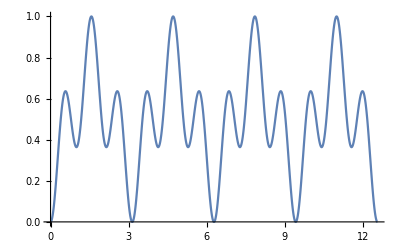

```mathematica
Plot[{P2[t]/.{ϕ->0,J->2,Jz->0.0,δ->4}},{t,0,4π}]
```

```mathematica
Gω=FullSimplify[Integrate[1/4 (2-Cos[t (-J+2 (Jz+δ))]-Cos[t (J+2 (Jz+δ))])Exp[-γ t]Exp[-ⅈ ω t],{t,0,∞},Assumptions->{γ>0,ω∈Reals,δ∈Reals,J ∈Reals, Jz ∈ Reals}]]
```

-1/(4 (1+(J-2 (Jz+δ))^2/(γ+ⅈ ω)^2) (γ+ⅈ ω))-1/(4 (1+(J+2 (Jz+δ))^2/(γ+ⅈ ω)^2) (γ+ⅈ ω))+1/(2 γ+2 ⅈ ω)

```mathematica
Fω=FullSimplify[ComplexExpand[Gω* Gω],Assumptions->{γ>0,δ∈Reals,}]
```

(J^8-2 J^6 (-γ^2+8 (Jz+δ)^2+ω^2)-8 J^2 (Jz+δ)^2 (32 Jz^4+4 Jz^2 γ^2-γ^4+128 Jz^3 δ+8 Jz γ^2 δ+192 Jz^2 δ^2+4 γ^2 δ^2+128 Jz δ^3+32 δ^4-2 (γ^2+2 (Jz+δ)^2) ω^2-ω^4)+16 (Jz+δ)^4 ((γ^2+4 (Jz+δ)^2)^2-2 (2 Jz-γ+2 δ) (2 Jz+γ+2 δ) ω^2+ω^4)+J^4 (96 Jz^4-8 Jz^2 γ^2+γ^4+384 Jz^3 δ-16 Jz γ^2 δ+576 Jz^2 δ^2-8 γ^2 δ^2+384 Jz δ^3+96 δ^4+2 (γ^2+4 (Jz+δ)^2) ω^2+ω^4))/(4 (γ^2+ω^2) ((γ^2+(J-2 (Jz+δ))^2)^2-2 (J-2 Jz-γ-2 δ) (J-2 Jz+γ-2 δ) ω^2+ω^4) ((γ^2+(J+2 (Jz+δ))^2)^2-2 (J+2 Jz-γ+2 δ) (J+2 Jz+γ+2 δ) ω^2+ω^4))

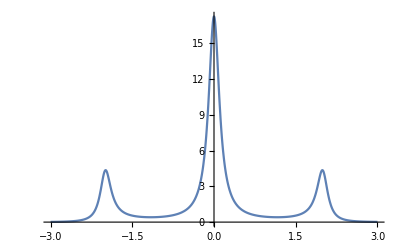

```mathematica
Plot[Fω/.{J->2,Jz->0.00,γ->0.12,δ->4/3600},{ω,-3,3},PlotRange->Full]
```

```mathematica
$Assumptions={J∈Reals,Jz∈Reals,ϕ∈Reals,t>0}
```

{J∈ℝ,Jz∈ℝ,ϕ∈ℝ,t>0}

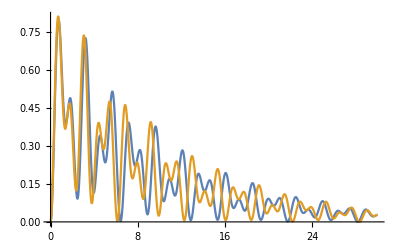

```mathematica
Block[{Δ=40,J=1,Jz=0.05,ϕ=0,γ=0.1,δ=4},
Plot[{Exp[-γ t]P1[t],Exp[-γ t]P2[t]},{t,0,3/γ},PlotRange->Full]]
```

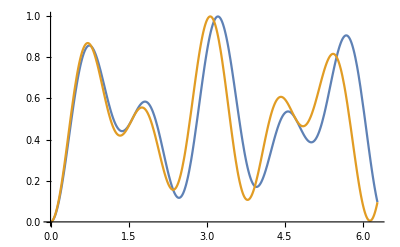

```mathematica
Block[{Δ=40,J=1,Jz=0.05,ϕ=0,δ=4},
Plot[{P1[t],P2[t]},{t,0,2π}]]
```

### Density matrix and master equation

In the experimental setup there is a lot of decay and qubit 3 is worse than qubit 2. This means that the whole system cannot be modeled by these simple interference patters and we cannot just impose an overall exponential---indeed, when population moves from 1 to 3 it has a stronger probability of decay, leading to faster losses.

The effective model for the master equation is

∂_t ρ=-ⅈ [H_eff,ρ]+L[ρ]=:L_tot[ρ]

with the dissipator

L[ρ]=∑ γ_i/2(2 σ_i^-ρσ_i^+-{σ_i^+σ_i^-,ρ})

We can solve this problem numerically with the help of Mathematica. First of all, we define a function that returns a matrix of symbols associated to the 4x4 components of the density matrix.

```mathematica
$Assumptions={J>=0,δ>=0,γ1>=0,γ2>=0}
```

{J≥0,δ≥0,γ1≥0,γ2≥0}

```mathematica
Clear[ρ];
Clear[ρ00,ρ01,ρ10,ρ11];
ρ[t_]=Table[Symbol["ρ"<>ToString[i]<>ToString[j]][t],{i,1,4},{j,1,4}]
```

{{ρ11[t],ρ12[t],ρ13[t],ρ14[t]},{ρ21[t],ρ22[t],ρ23[t],ρ24[t]},{ρ31[t],ρ32[t],ρ33[t],ρ34[t]},{ρ41[t],ρ42[t],ρ43[t],ρ44[t]}}

To define the dynamics, we need operators acting on each of the qubits individually.

```mathematica
σm={{0,0},{1,0}};
σp=σm†;
σz=σp.σm-σm.σp;
σ1m = KroneckerProduct[σm,IdentityMatrix[2]];
σ2m = KroneckerProduct[IdentityMatrix[2],σm];
σ1p = σ1m†;
σ2p =σ2m†;
σ1z=KroneckerProduct[{{1,0},{0,-1}},IdentityMatrix[2]];
σ2z=KroneckerProduct[IdentityMatrix[2],{{1,0},{0,-1}}];
```

To test the solutions, we need to define different initial states. The following are diagonal states:

```mathematica
P00 =KroneckerProduct[σm.σp,σm.σp];
P01=KroneckerProduct[σm.σp,σp.σm];
P10=KroneckerProduct[σp.σm,σm.σp];
P11=KroneckerProduct[σp.σm,σp.σm];
```

We can also use superposition states, with the help of Hadamard:

```mathematica
Hadamard={{1,1},{-1,1}}/√2;
Hadamard1= KroneckerProduct[Hadamard,IdentityMatrix[2]];
Hadamard2= KroneckerProduct[IdentityMatrix[2],Hadamard];
PX0=Hadamard1.P00.Hadamard1†;
PX1=Hadamard1.P01.Hadamard1†;
P0X=Hadamard1.P00.Hadamard1†;
P1X=Hadamard1.P10.Hadamard1†;
```

With the operators, it becomes easier to define the effective Hamiltonian

```mathematica
Heff=J(σ1p . σ2m + σ1m . σ2p)+δ/2(σ1z+σ2z);
Heff//MatrixForm
```

(δ | 0 | 0 | 0
0 | 0 | J | 0
0 | J | 0 | 0
0 | 0 | 0 | -δ)

and also the dissipation term.

```mathematica
L[ρ_]=γ1/2(2σ1m.ρ.σ1p-σ1p.σ1m.ρ-ρ.σ1p.σ1m)+γ2/2(2σ2m.ρ.σ2p-σ2p.σ2m.ρ-ρ.σ2p.σ2m);
```

Together, they create the total Lindbladian.

```mathematica
Ltot[ρ_]=-ⅈ (Heff . ρ - ρ . Heff) + L[ρ];
```

Let us define a function that, given an initial state, ρ0, solves the dynamics.

```mathematica
Clear[MESol];
MESol[ρ0_]:=Module[
{ (* Equations for the dynamics and the initial state *)
equations=Flatten[ρ'[t]]==Flatten[Ltot[ρ[t]]]//Thread,
initial=Flatten[ρ[0]]==Flatten[ρ0] //Thread,
unknowns=Flatten[ρ[t]]
},
Module[{Solution=FullSimplify[DSolve[{equations,initial},unknowns,t]]},
ρ[t]/.Solution[[1]]]]
```

We can also define observables in terms of these solutions. For instance, the σ_z expected values over the first and second qubits or the probabilities of excitation

```mathematica
Clear[MESolZ1,MESolZ2,MESolP1,MESolP2];
MESolZ1[ρ0_]:=FullSimplify[Tr[σ1z.MESol[ρ0]],{J>0,δ∈Reals,γ1>=0,γ2>=0}];
MESolZ2[ρ0_]:=FullSimplify[Tr[σ2z.MESol[ρ0]],{J>0,δ∈Reals,γ1>=0,γ2>=0}];
MESolP1[ρ0_]:=FullSimplify[Tr[(σ1p.σ1m).MESol[ρ0]],{J>0,δ∈Reals,γ1>=0,γ2>=0}];
MESolP2[ρ0_]:=FullSimplify[Tr[(σ2p.σ2m).MESol[ρ0]],{J>0,δ∈Reals,γ1>=0,γ2>=0}];
```

The 00 state does not evolve under this model:

```mathematica
MESol[P00]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1)

If we have no disipation, the 01 state oscillates, as reflected in the value of σ_z

```mathematica
Block[{γ1=0,γ2=0},
MESolZ2[P01]]
```

Cos[2 J t]

When there is dissipation, this depends on whether the dissipations are identical or not. In the first case, we have the function we were fitting:

```mathematica
Block[{γ2=γ1},
Expand[MESolZ2[P01]]]
```

-1/2+ⅇ^(-t γ1)/2+ⅇ^(-t γ1) Cos[2 J t]

In the second case, it’s more complicated. For instance, the population in the second qubit is

```mathematica
MESolP2[P10]
```

(16 ⅇ^(-1/2 t (γ1+γ2)) J^2 Sinh[1/4 t √(-16 J^2+(γ1-γ2)^2)]^2)/(-16 J^2+(γ1-γ2)^2)

And in the first qubit

```mathematica
MESolP1[P10]
```

1/(2 (-16 J^2+(γ1-γ2)^2))ⅇ^(-1/2 t (γ1+√(-16 J^2+(γ1-γ2)^2)+γ2)) (-8 (1+ⅇ^(1/2 t √(-16 J^2+(γ1-γ2)^2)))^2 J^2+(γ1-γ2) ((1+ⅇ^(t √(-16 J^2+(γ1-γ2)^2))) γ1+√(-16 J^2+(γ1-γ2)^2)-γ2-ⅇ^(t √(-16 J^2+(γ1-γ2)^2)) (√(-16 J^2+(γ1-γ2)^2)+γ2)))

```mathematica
Clear[Protocol1P];
Protocol1P=Tr[Hadamard1†.(σ1p.σ1m).Hadamard1.MESol[PX0]];
```

```mathematica
aux=Limit[Protocol1P,γ2->γ1,Direction->"FromAbove"];
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

```mathematica
aux2=Block[{γ2=γ1},Tr[Hadamard1†.(σ1p.σ1m).Hadamard1.MESol[PX0]]];
```

```mathematica
FullSimplify[aux2]
```

1/4 ⅇ^(-(t γ1)/2) (2 Cos[J t] Cos[t δ]+2 Cosh[(t γ1)/2]+Sinh[(t γ1)/2])

```mathematica
FullSimplify[aux-aux2]
```

0

```mathematica
Clear[Protocol2P];
Protocol2P=Tr[Hadamard1†.(σ1p.σ1m).Hadamard1.MESol[PX1]];
```

```mathematica
aux=Limit[Protocol2P,γ2->γ1,Direction->"FromAbove"];
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

```mathematica
aux2=Block[{γ2=γ1},Tr[Hadamard1†.(σ1p.σ1m).Hadamard1.MESol[PX1]]];
```

```mathematica
FullSimplify[aux2]
```

1/(8 (4 J^2+γ1^2))ⅇ^(-t γ1) (4 Cos[t δ] Cosh[(t γ1)/2] ((4 J^2+γ1^2) Cos[J t]+2 J γ1 Sin[J t])-16 J^2 Cos[J t] Cos[t δ] Sinh[(t γ1)/2]+(4 J^2+γ1^2) (2+2 Cosh[t γ1]+Sinh[t γ1]))

```mathematica
FullSimplify[aux-aux2]
```

0

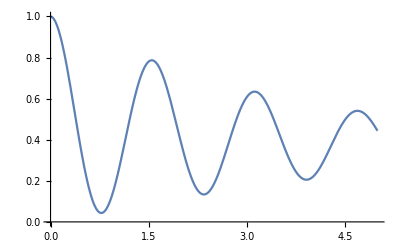

```mathematica
Block[{γ2=10,γ1=0.1,J=1,δ=4},
Plot[Protocol1P,{t,0,5}]]
```

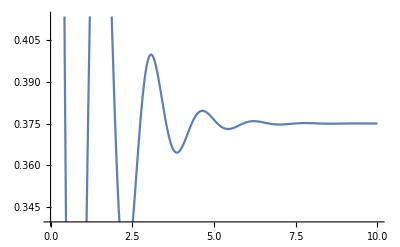

```mathematica
Block[{γ2=10,γ1=0.1,J=2,δ=4},
Plot[Protocol1P,{t,0,10}]]
```